```mathematica
ClearAll["Global`*"];

(* 
Runs the simulation remotely over ssh.
paramsList contains parameters in a nested array, in the form of:
	{{Subscript[Δ, 1], Subscript[Δ, 2], ϵ, sym, δ, λ, simTime}, ...}
where 'sym' is a boolean 0 or 1 specifying whether the noise is asymmetric (0 = symmetric),
and 'simTime' is the simulation time, calculated automatically from parameters if it is 0
 *)
RunSimulationHist[paramsList_,numInvocations_:Integer,xlow_:NumericQ,xhigh_:NumericQ]:=Module[{lines,inputString,output,ys,asd},lines=(StringRiffle[ToString/@Join[#,{numInvocations,N[xlow],N[xhigh]}]," "]&)/@paramsList;
inputString=StringRiffle[Prepend[lines,ToString[Length[paramsList]]],"\n"];
output=RunProcess[{"ssh", "compute2", "~/projects/kinetic/bin/pdmp_example"},"StandardOutput",inputString];
asd=StringSplit[StringTrim[output ]];
ys=Internal`StringToMReal/@asd;
ys];

(* stationary probability distribution *)
Π[x_,Δ1_, Δ2_, ϵ_,λ_, δ_]:=x^(-2*λ*((Δ2 + δ*ϵ)/(Δ2^2 - ϵ^2)) - 1)*(1 - x)^(2*λ*((Δ1 + δ*ϵ)/(Δ1^2 - ϵ^2)) - 1)*Abs[(Δ1 - Δ2)*x + Δ2 + ϵ]^(λ*(1 - δ)*((Δ1 - Δ2)/(Δ1 + ϵ)/(Δ2 + ϵ)) - 1)*
  Abs[(Δ1 - Δ2)*x + Δ2 - ϵ]^(λ*(1 + δ)*((Δ1 - Δ2)/(Δ1 - ϵ)/(Δ2 - ϵ)) - 1); 
Exps[Δ1_, Δ2_, ϵ_,λ_, δ_]:={
(2*λ*((Δ1 + δ*ϵ)/(Δ1^2 - ϵ^2)) - 1), 
(λ*(1 + δ)*((Δ1 - Δ2)/(Δ1 - ϵ)/(Δ2 - ϵ)) - 1),
(ϵ^2-Δ1^2+2λ Δ1)/ (2λ ϵ),  (Δ2 - ϵ)(ϵ-Δ1)/λ/(Δ2-Δ1)-1}; 
(* stationary probability distribution for asymmetric noise *)
Πas[x_,Δ1_, Δ2_, ϵ_, λ_, δ_]:= x^(-(2λ Δ2 - λ(1-δ)ϵ)/  Δ2 /( Δ2-ϵ) - 1)*(1-x)^((2λ Δ1 - λ(1-δ)ϵ)/  Δ1 /( Δ1-ϵ) - 1)*((Δ1-Δ2)x+Δ2)^(λ(1-δ)(Δ1-Δ2)/Δ1 / Δ2 - 1)*(-(Δ1-Δ2)x-Δ2+ϵ)^(λ(1+δ)(Δ1-Δ2)/(Δ1-ϵ) / (Δ2-ϵ) - 1); 

(* simulation time and number of simulations for trajectory drawing *)
Tf=100.0;
numSims = 500;
(* get sample trajectories for a specified set of parameters *)
getData[Δ1_,Δ2_, ϵ_, δ_, λ_, xl_, xh_] := Block[{left, right, sims, tab,f,g, Simulate2}, 
f[x_]=x*(1-x)*(Δ2+(Δ1-Δ2) x);
       g[x_]=x*(1-x)*ϵ;
Simulate2=ParametricNDSolve[{
y'[t]==f[y[t]]+ξ[t]*g[y[t]],
h'[t]==2*λ67,
WhenEvent[h[t]>=tn[t],{ξ[t]->If[RandomReal[]<=(1-δ1)/2,-1,1],
h[t]->0,tn[t]->RandomVariate[ExponentialDistribution[1]]}],
tn[0]== tn0,
y[0]==y0,
h[0]==0,
ξ[0]==ξ0},
{y,h, ξ},{t,0,Tf},
{y0,ξ0,λ67,δ1, tn0},(*parameters*)
DiscreteVariables->{ξ,tn}];
left=(Δ2-ϵ)/(Δ2-Δ1)+10^-4;
	right=(Δ2+ϵ)/(Δ2-Δ1)-10^-4;
sims = ParallelTable[
(y[xl + (xh-xl)RandomReal[], RandomChoice[{-1, 1}], λ, δ , RandomVariate[ExponentialDistribution[1]]]) /. Simulate2, 
{numSims}];
tab = Table[
{t, sims[[i]][t]}, 
{t, 0, Tf, Tf/100},
{i, 0, numSims}
];
Transpose[tab]
 ]

α=0.5;
β=1.0;
ϵ=0.75;
numInvoc = 10000;
λ=2.0;
δ11=0.0;
δ12=-0.7;
δ13=-0.95;
δ14=-0.83;

xm[α_,β_,ϵ_]:=(β-ϵ)/(β-α)+10^-6;
xp[α_,β_,ϵ_]:=1.0-10^-6;

left = xm[α,β,ϵ];
right=xp[α,β,ϵ];

C1 = NIntegrate[Π[t,α,β,ϵ,λ,δ11], {t, left, right}];
C2 = NIntegrate[Π[t,α,β,ϵ,λ,δ12], {t, left, right}];
C3 = NIntegrate[Π[t,α,β,ϵ,λ,δ13], {t, left, right}];
C4 = NIntegrate[Π[t,α,β,ϵ,λ,δ14], {t, left, right}];

tab =Table[{x,Π[x,α,β,ϵ,λ,δ11]/C1}, {x, left, right,(right-left)/50}];
tab2 = RunSimulationHist[{{ α,β, ϵ,0, δ11,λ, 0  }}, numInvoc, 0, 1];

tab3 =Table[{x,Π[x,α,β,ϵ,λ, δ12]/C2}, {x, left, right,(right-left)/50}];
tab4 =  RunSimulationHist[{{ α,β, ϵ,0, δ12,λ, 0  }}, numInvoc, 0, 1];

tab5 =Table[{x,Π[x,α,β,ϵ,λ,δ13]/C3}, {x, left, right,(right-left)/50}];
tab6 =  RunSimulationHist[{{ α,β, ϵ,0, δ13,λ, 0  }}, numInvoc, 0, 1];

Exps[α,β,ϵ,1,0.875]
tab7 =Table[{x,Π[x,α,β,ϵ,λ,δ14]/C4}, {x, left, right,(right-left)/50}];
tab8 =  RunSimulationHist[{{ α,β, ϵ,0, δ14,λ, 0  }}, numInvoc, 0, 1];
```

{-8.4,14.,0.875,-0.875}

```mathematica
data1 = getData[α,β,ϵ, 0, 2.0, 0, 1];
data2 = getData[α,β,ϵ, -0.7, 2.0, 0, 1];
data3 = getData[α,β,ϵ, -0.95, 2.0, 0, 1];
data4 = getData[α,β,ϵ, -0.83, 2.0, 0, 1];
```

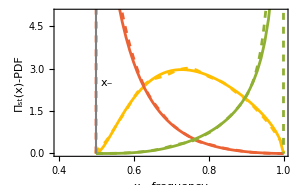

./Documents/Dominance/DominancePlots.svg

```mathematica
plt= Show[
SmoothHistogram[tab8, 0.02, "PDF", PlotStyle->{ColorData[97,8], Dashed},PlotRange->{{left, right}, Full}], 
ListLinePlot[tab7, PlotStyle->{ColorData[97,8]},PlotRange->{{0, 1},Full}],
SmoothHistogram[tab6, 0.02, "PDF", PlotStyle->{ColorData[97,4], Dashed},PlotRange->{{left, right}, Full}], 
ListLinePlot[tab5, PlotStyle->{ColorData[97,4]},PlotRange->{{0, 1},Full}],
SmoothHistogram[tab4, 0.02, "PDF", PlotStyle->{ColorData[97,3], Dashed},PlotRange->{{left, right},Full}], 
ListLinePlot[tab3, PlotStyle->{ColorData[97,3]},PlotRange->{{0, 1}, Full}],
(* SmoothHistogram[tab2, 0.02, "PDF", PlotStyle->{ColorData[97,1], Dashed},PlotRange->{{left, right}, Full}], 
ListLinePlot[tab, PlotStyle->{ColorData[97,1]},PlotRange->{{0, 1}, Full}], *)
ListLinePlot[{{left, 0}, {left, 10}}, PlotStyle->{Gray, Thickness[0.005]},PlotRange->{{0, 1}, Full}],
PlotRange->{{0.4, 1}, {0,5}}, Frame->True, FrameLabel->{"x - frequency", "Π_st(x)-PDF"}, BaseStyle->{FontSize->14}, ImageSize->300,
Epilog->Style[Text["x_-",{0.53, 2.5}],14]
]
Export["./Documents/Dominance/DominancePlots.svg", plt]
```

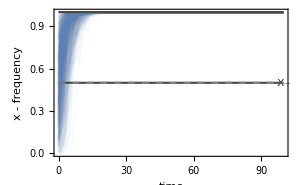

./Documents/Dominance/DominanceTrajectoriesSymmetric.svg

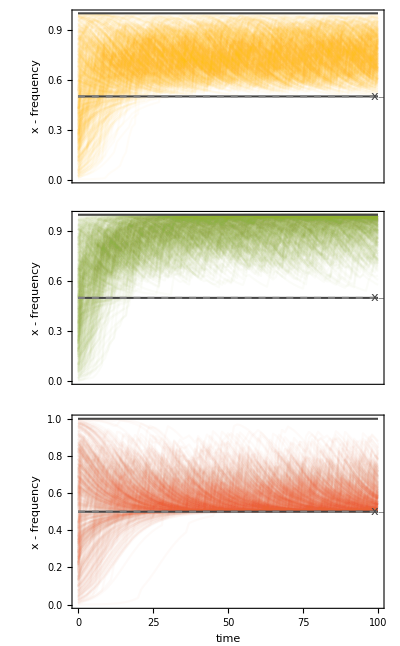

./Documents/Dominance/DominanceTrajectories.svg

```mathematica
sz=300;
labelEpilog[Tf_,left_,right_]:={
Text[Style[Subscript["x","-"],DarkGray,13],{Tf,left},{-2.5,0}]};

getPlot[data_,l_, ax1_, ax2_]:=Block[{left, right},
left=xm[α,β,ϵ];
right=xp[α,β,ϵ];
Show[
ListLinePlot[data,PlotStyle->Directive[ColorData[97,l],Opacity[0.03],Thickness[0.005]],Frame->True,FrameTicks->{If[ax1!=None, True, False],True},BaseStyle->{FontSize->14},ImageSize->sz, PlotRange->{{0, Tf}, {0, 1}}],
ListLinePlot[{{{0,left},{Tf,left}},{{0,right},{Tf,right}},{{0,0.5},{Tf,0.5}}},PlotStyle->{Directive[DarkGray,Thickness[0.005]],Directive[DarkGray,Thickness[0.005]],Directive[Gray,Dashed,Thickness[0.005]]}],Epilog->labelEpilog[Tf,left,right],ImagePadding->{{Automatic,40},{Automatic,Automatic}},PlotRangeClipping->False,FrameLabel->{
ax1, ax2},
PlotRange->{{0, Tf}, {0, 1}}
]];
symplot=
getPlot[data1,1, "time","x - frequency"]
Export["./Documents/Dominance/DominanceTrajectoriesSymmetric.svg", symplot]

finalplt=Show[GraphicsColumn[{
getPlot[data4,8, None, "x - frequency"],
getPlot[data2,3, None, "x - frequency"],
getPlot[data3,4, "time", "x - frequency"]
}, Spacings->Scaled[0.01]]]
Export["./Documents/Dominance/DominanceTrajectories.svg", finalplt]
```

```mathematica
δm=-α/ϵ
tab =ParallelTable[{x,δ,Π[x,α,β,ϵ,λ,δ] /  NIntegrate[Π[t,α,β,ϵ,λ,δ], {t, left, right}] }, {x, left, right, 0.01}, {δ, -0.9, δm+0.02, 0.01}];
plot = Show[ListPlot3D[
Flatten[tab,1], 
PlotRange->{Full, Full, {0,5}},
ColorFunction->Function[{x,y,z},ColorData["RedBlueTones"][y]],
AxesLabel->{Style["x - frequency", Bold],Style[ "δ - bias", Bold], Style["Π_st(x)-PDF", Bold]}, 
Ticks->{True,True,True},
Axes->{True,True,True},
 Boxed->False,
AxesEdge->{{-1,-1},{-1,-1},{-1,1}},
ViewPoint->{-1.6260733668645397,-2.507835053431862,1.5863948910508319},
BaseStyle->{FontSize->14}, ImageSize->400], ImagePadding->90]
Export["./Documents/Dominance/Dominance3D.svg", plot]
```

-0.666667

-Graphics3D-

./Documents/Dominance/Dominance3D.svg

```mathematica
ViewPoint /. AbsoluteOptions[-Graphics3D-]
```

{-1.62607,-2.50784,1.58639}

```mathematica
ClearAll["Global`*"];
Clear[Subscript];
ml=10^-4;
mr=10^-4;
MFPT[α_,β_,ϵ_,λ_,x0_]:=Module[{left,right,xl,xr},left=(β-ϵ)/(β-α);
right=1;
xl=left+ml;
xr=right-mr;
sol=NDSolve[
{
(x (1-x) ((α-β) x+β+ϵ)) Tp'[x]-λ*Tp[x]+λ*Tm[x]==-1,
(x (1-x) ((α-β) x+β-ϵ)) Tm'[x]+λ*Tp[x]-λ*Tm[x]==-1,
Tp[xr]==0,
Tm[xl]==1/λ+Tp[xl]
},{Tp,Tm},{x,xl,xr}];
(Tp[x0]+Tm[x0])/2/. sol];
t[α_,β_,x_]:=1/β Log[x]-1/α Log[1-x]-(α-β)/α/β Log[Abs[β+(α-β) x]];
FPTdet[α_,β_,x_]:=t[α,β,1-mr]-t[α,β,x];
sample[α_,β_,ϵ_]:=((β-ϵ)/(β-α)+ 1) / 2;
hittime[α_, β_, ϵ_,λ_]:=MFPT[α, β,ϵ,λ,sample[α,β,ϵ]];
hittime2[α_,β_, ϵ_] := FPTdet[α,β,sample[α,β,ϵ]];
```

```mathematica
tab = Table[
ParallelTable[{λ,hittime[α, 1.0, 0.75, λ] [[1]] }, {λ, 0.01, 1.5, 0.01}],
{α, 0.1, 0.4, 0.1}];
tab2 =  Table[
Table[{λ,hittime2[α, 1.0, 0.75]  }, {λ, 0.01, 1.5, 0.01}],
{α, 0.1, 0.4, 0.1}];

graphLambdaToRate = ListLinePlot[Join[tab2, tab],
PlotStyle->{Directive[ColorData[97, 1], Dashed], Directive[ColorData[97, 2], Dashed],Directive[ColorData[97, 3], Dashed],Directive[ColorData[97, 4], Dashed] ,
ColorData[97, 1], ColorData[97, 2], ColorData[97, 3], ColorData[97, 4]},
BaseStyle->{FontSize->14}, 
PlotLabels->Join[Table[None, {i, 4}],(StringJoin["Δ_1 = ",ToString[#]] & /@ Range[0.1, 0.4, 0.1])], 
FrameLabel->{"λ - switch rate", "Φ(λ) - MFPT"}, 
Frame->True, 
ImageSize->Medium]
Export["./Documents/Dominance/DominanceMFPTLambdaDependence.svg", graphLambdaToRate]
```

-Graphics-

./Documents/Dominance/DominanceMFPTLambdaDependence.svg

ParametricNDSolveValue::berr: The scaled boundary value residual error of 5.09787 indicates that the boundary values are not satisfied to specified tolerances. Returning the best solution found.

ParametricNDSolveValue::berr: The scaled boundary value residual error of 1.21038 indicates that the boundary values are not satisfied to specified tolerances. Returning the best solution found.

ParametricNDSolveValue::berr: The scaled boundary value residual error of 5.33407 indicates that the boundary values are not satisfied to specified tolerances. Returning the best solution found.

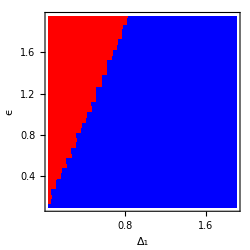

./Documents/Dominance/DominanceHeatmapAlphaEpsilon.svg

```mathematica
(* THE HEATMAP FOR MFPT *)
λmi=0.5;
λmx =2.0;

getMode[Δ1_, Δ2_, ϵ_] := Module[{tab},
left=(Δ2-ϵ)/(Δ2-Δ1);
right=1;
xl=left+ml;
xr=right-mr;
sol2=ParametricNDSolveValue[
{
(x (1-x) ((Δ1-Δ2) x+Δ2+ϵ)) Tp'[x]-λ*Tp[x]+λ*Tm[x]==-1,
(x (1-x) ((Δ1-Δ2) x+Δ2-ϵ)) Tm'[x]+λ*Tp[x]-λ*Tm[x]==-1,
Tp[xr]==0,
Tm[xl]==1/λ+Tp[xl]
},{Tp,Tm},{x,xl,xr},  {λ}];
x0=sample[Δ1, Δ2,ϵ];
tab = Table[((sol2[λ][[1]][x0]+sol2[λ][[2]][x0])/2), {λ, λmi, λmx, 0.25}];
If[OrderedQ[tab, Greater], 0, 1]
];
β=2.0;
tab=Flatten[ParallelTable[{α, ϵ, getMode[α,β, ϵ]},{α, 0.05, β-0.1, 0.05},{ϵ,α+0.05, β-0.05, 0.05}], 1];
colors={White, Blue,Red,Darker[Green],Orange};
discreteColor[z_]:=Which[z<=-1, colors[[1]],z<=0,colors[[2]],z<=1,colors[[3]],z<=2,colors[[4]],z<=3,colors[[5]]];
pl1=ListDensityPlot[
tab,(*1. Define the split at zero*)
PlotRange->All,(*2. Color regions:First color is disc<0,Second color is disc>0*)
(*RegionFunction->Function[{β,λ},Max[(α β+α ϵ+β ϵ+ϵ^2)/(α-β),(α β-α ϵ-β ϵ+ϵ^2)/(α-β)]<=λ<=8],*)(*Aesthetics*)
InterpolationOrder->0,
Frame->True,
ColorFunctionScaling->False,
FrameLabel->{"Δ_1","ϵ"},
BaseStyle->{FontSize->14},
ImageSize->250,
ColorFunction->discreteColor]
Export["./Documents/Dominance/DominanceHeatmapAlphaEpsilon.svg", pl1]
```

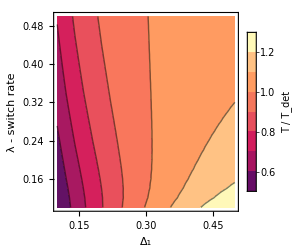

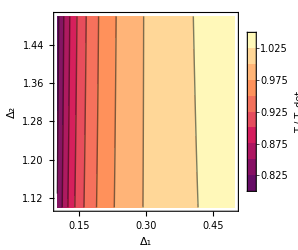

./Documents/Dominance/DominanceContMapAlphaLambda.svg

./Documents/Dominance/DominanceContMapAlphaBeta.svg

```mathematica
sz = 250;

graph1 =  ListContourPlot[
{Flatten[ParallelTable[{α,λ,Block[{ϵ,β}, 
ϵ=0.75;
β=1.0;
(hittime[α,β,ϵ,λ]/hittime2[α,β,ϵ])[[1]]
]}, {α, 0.1, 0.5, 0.02}, {λ, 0.1, 0.5, 0.02}], 1]}, PlotLayout->Row,
Frame->True, Axes->True, FrameLabel->{Subscript[Δ, 1],"λ - switch rate"}, PlotLegends->BarLegend[Automatic,LegendLabel->"T / T_det",LegendMarkerSize->{40,sz/2}],
 ImageSize->sz, BaseStyle->{FontSize->14}
]
graph2 = ListContourPlot[
{ Flatten[ParallelTable[{α,β,Block[{ϵ,λ}, 
ϵ=0.75;
λ=1.0;
(hittime[α,β,ϵ,λ]/hittime2[α,β,ϵ])[[1]]
]}, {α, 0.1, 0.5, 0.02}, {β, 1.1, 1.5, 0.02}], 1]}, PlotLayout->Row,
Frame->True, Axes->True, FrameLabel->{Subscript[Δ, 1],Subscript[Δ, 2]}, PlotLegends->BarLegend[Automatic,LegendLabel->"T / T_det",LegendMarkerSize->{40,sz/2}], 
 ImageSize->sz, BaseStyle->{FontSize->14}]

Export["./Documents/Dominance/DominanceContMapAlphaLambda.svg",graph1]
Export["./Documents/Dominance/DominanceContMapAlphaBeta.svg", graph2]
```

```mathematica
ClearAll["Global`*"];
sz=250;
Π[x_,Δ1_, Δ2_, ϵ_,λ_, δ_]:=x^(-2 λ (Δ2+δ ϵ)/(Δ2^2-ϵ^2)-1) ( 1-x)^(2 λ (Δ1+δ ϵ)/(Δ1^2-ϵ^2)-1) Abs[(Δ1-Δ2) x+Δ2+ϵ]^(λ (1-δ) (Δ1-Δ2)/(Δ1+ϵ)/(Δ2+ϵ)-1) Abs[(Δ1-Δ2) x+Δ2-ϵ]^(λ (1+δ) (Δ1-Δ2)/(Δ1-ϵ)/(Δ2-ϵ)-1); 
Πas[x_,Δ1_, Δ2_, ϵ_, λ_, δ_]:= x^(-(2λ Δ2 - λ(1-δ)ϵ)/  Δ2 /( Δ2-ϵ) - 1)*(1-x)^((2λ Δ1 - λ(1-δ)ϵ)/  Δ1 /( Δ1-ϵ) - 1)*((Δ1-Δ2)x+Δ2)^(λ(1-δ)(Δ1-Δ2)/Δ1 / Δ2 - 1)*(-(Δ1-Δ2)x-Δ2+ϵ)^(λ(1+δ)(Δ1-Δ2)/(Δ1-ϵ) / (Δ2-ϵ) - 1); 
(*2. Master Equations*)
extrema[x_,α_, β_, ϵ_,λ_]:=(-4 x^3 (α-β)^2+β^2-β ϵ+3 x^2 (α-β) (α-3 β+ϵ)+2 β λ-ϵ λ-2 x β (3 β-2 ϵ+λ)+2 x α (2 β-ϵ+λ));
extremaDx[x_,α_,β_,ε_,λ_]:=Evaluate[D[extrema[z,α,β,ε,λ],z]/. z->x];
xm[α_,β_,ϵ_]:=(β-ϵ)/(β-α);
xp[α_,β_,ϵ_]:=1.0;
(*3. Numerical Root Counter*)
countExtrema[α_?NumericQ,β_?NumericQ,ϵ_?NumericQ,λ_?NumericQ]:=Module[{xmm,xpp,roots, nr},xmm=xm[α,β,ϵ];
xpp=xp[α,β,ϵ];
roots=x/. NSolve[extrema[x,α,β,ϵ,λ]==0&&xmm<=x<=xpp,x,Reals];
nr = Length[roots];
If[((2λ α - λ ϵ)/  α /( α-ϵ) - 1)<-1 , -1,
If[nr==3, 3, If[nr==2,
If[((2λ α - λ ϵ)/  α /( α-ϵ) - 1)>0 , 2, 6],
If[nr==1, 
If[((2λ α - λ ϵ)/  α /( α-ϵ) - 1)>0 , 1, 5], 
If[((2λ α - λ ϵ)/  α /( α-ϵ) - 1)>0 , 0, 4]
]
]
]
]
];
```

```mathematica
(* 
Gray -> Full Defector,
Light Green -> M shape (3 extrema),
Light Blue -> 2 extrema, 0 at 1, inf at eps-,
Dark Blue -> 2 extrema, inf at 1, 0 at eps-,
Light Yellow -> 1 Extrema, 0 at both, local max,
Dark Yellow -> 1 Extrema, inf at both, local min,
Dark Red -> 0 Extrema, inf at 
*)
colorFn = Function[z,Lighter[Switch[Round[z], -1, Darker[ColorData[97, 4]], 
0, Lighter[ColorData[97, 4]], 4, Darker[ColorData[97, 4]],
1, Lighter[ColorData[97, 8]], 5,  Darker[ColorData[97, 8]],
2, Lighter[ColorData[97, 1]], 6,  Darker[ColorData[97, 1]],
3, Lighter[ColorData[97, 3]], 7,  Darker[ColorData[97, 3]]
]]];
{0, Lighter[ColorData[97, 4]], 4, Darker[ColorData[97, 4]],
1, Lighter[ColorData[97, 8]], 5,  Darker[ColorData[97, 8]],
2, Lighter[ColorData[97, 1]], 6,  Darker[ColorData[97, 1]],
3, Lighter[ColorData[97, 3]], 7,  Darker[ColorData[97, 3]]}
Δ1=0.1;
ϵ=0.75;
(*4. High-Resolution Parallel Grid Generation*)
gridData=Flatten[ParallelTable[{Δ2,λ,countExtrema[Δ1, Δ2, ϵ,λ]},{Δ2,1.0,1.5,0.002},{λ,0.05,0.4,0.002}],1];
(*5. Render Plot with Exact Black/Orange Journal Styling*)
plot1=ListDensityPlot[gridData,InterpolationOrder->0,ColorFunction->colorFn,ColorFunctionScaling->False,
Frame->True,
FrameLabel->{"Δ_2","λ - switch rate"},
BaseStyle->{FontSize->14}, ImageSize->sz,
ImageSize->Medium]

Export["./Documents/Dominance/DominanceExtrema(A=0.1,E=0.75).svg", plot1]
```

{0,RGBColor[0.9483506666666667, 0.5904173333333333, 0.472786],4,RGBColor[0.6150173333333333, 0.25708400000000003, 0.13945266666666667],1,RGBColor[1, 0.8333333333333334, Rational[1, 3]],5,RGBColor[Rational[2, 3], 0.5, 0],2,RGBColor[0.5789446666666667, 0.671186, 0.806532],6,RGBColor[0.24561133333333335, 0.3378526666666667, 0.4731986666666667],3,RGBColor[0.7067873333333333, 0.7943793333333333, 0.46325666666666665],7,RGBColor[0.37345400000000006, 0.461046, 0.12992333333333334]}

-Graphics-

./Documents/Dominance/DominanceExtrema(A=0.1,E=0.75).svg

```mathematica
α=0.1;
β=1.0;
ϵ=0.6;
λ=0.19;
((2λ α - λ ϵ)/  α /( α-ϵ) - 1)
(λ(1+0)(α-β)/(α-ϵ) / (β-ϵ) - 1)
countExtrema[α,β,ϵ,λ]
ListLinePlot[Table[{x, Πas[x,α,β,ϵ,λ, 0]},
 {x, xm[α,β,ϵ], xp[α,β,ϵ], 0.001}]]
```

0.52

```mathematica
countExtrema[0.1,1,0.5,0.19]
```

2

```mathematica
Δ2=1.0;
Δ1=0.1;
(*4. High-Resolution Parallel Grid Generation*)
gridData=Flatten[ParallelTable[{ϵ,λ,countExtrema[Δ1, Δ2, ϵ,λ]},{ϵ,0.11,0.99,0.002},{λ,0.1,0.4,0.002}],1];
(*5. Render Plot with Exact Black/Orange Journal Styling*)
```

```mathematica
plot1=ListDensityPlot[gridData,InterpolationOrder->0,ColorFunction->colorFn,ColorFunctionScaling->False,
Frame->True,
FrameLabel->{"ϵ","λ - switch rate"},
BaseStyle->{FontSize->14}, ImageSize->sz,
ImageSize->Medium,
Epilog->{
{Directive[Dashed, Black],
Thickness[0.008],
Line[{{2*Δ1,0.1},{2*Δ1,0.4}}]},
Text[Style["2Δ_1",FontSize->14],
{2*Δ1,-0.05},(*{x,y} position*)
{-1,0}       (*Offset:left-aligned horizontally,centered vertically*)]
}]

Export["./Documents/Dominance/DominanceExtrema(A=0.1,B=1.0).svg", plot1]
```

-Graphics-

./Documents/Dominance/DominanceExtrema(A=0.1,B=1.0).svg

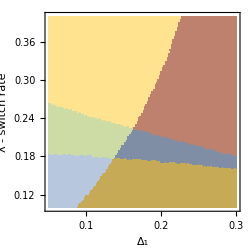

./Documents/Dominance/DominanceExtrema(B=1.0,E=0.75).svg

```mathematica
Δ2=1.0;
ϵ=0.75;
(*4. High-Resolution Parallel Grid Generation*)
gridData=Flatten[ParallelTable[{Δ1,λ,countExtrema[Δ1, Δ2, ϵ,λ]},{Δ1,0.05,0.3,0.002},{λ,0.1,0.4,0.002}],1];
(*5. Render Plot with Exact Black/Orange Journal Styling*)
plot1=ListDensityPlot[gridData,InterpolationOrder->0,ColorFunction->colorFn,ColorFunctionScaling->False,
Frame->True,
FrameLabel->{"Δ_1","λ - switch rate"},
BaseStyle->{FontSize->14}, ImageSize->sz,
ImageSize->Medium ,
FrameTicks->{{Automatic,Automatic},{Charting`ScaledTicks[{Identity,Identity}],None}}]

Export["./Documents/Dominance/DominanceExtrema(B=1.0,E=0.75).svg", plot1]
```

```mathematica
ClearAll["Global`*"];

RunSimulationHist[paramsList_,numInvocations_:Integer,xlow_:NumericQ,xhigh_:NumericQ]:=Module[{lines,inputString,output,ys,asd},lines=(StringRiffle[ToString/@Join[#,{numInvocations,N[xlow],N[xhigh]}]," "]&)/@paramsList;
inputString=StringRiffle[Prepend[lines,ToString[Length[paramsList]]],"\n"];
output=RunProcess[{"ssh", "compute2", "~/projects/kinetic/bin/pdmp_example"},"StandardOutput",inputString];
asd=StringSplit[StringTrim[output ]];
ys=Internal`StringToMReal/@asd;
ys];


err=10^-7;
numInvoc = 10000;

Πas[x_,Δ1_, Δ2_, ϵ_, λ_, δ_]:= x^(-(2λ Δ2 - λ(1-δ)ϵ)/  Δ2 /( Δ2-ϵ) - 1)*(1-x)^((2λ Δ1 - λ(1-δ)ϵ)/  Δ1 /( Δ1-ϵ) - 1)*((Δ1-Δ2)x+Δ2)^(λ(1-δ)(Δ1-Δ2)/Δ1 / Δ2 - 1)*(-(Δ1-Δ2)x-Δ2+ϵ)^(λ(1+δ)(Δ1-Δ2)/(Δ1-ϵ) / (Δ2-ϵ) - 1); 
Π[x_,Δ1_, Δ2_, ϵ_,λ_, δ_]:=x^(-2*λ*((Δ2 + δ*ϵ)/(Δ2^2 - ϵ^2)) - 1)*(1 - x)^(2*λ*((Δ1 + δ*ϵ)/(Δ1^2 - ϵ^2)) - 1)*Abs[(Δ1 - Δ2)*x + Δ2 + ϵ]^(λ*(1 - δ)*((Δ1 - Δ2)/(Δ1 + ϵ)/(Δ2 + ϵ)) - 1)*
  Abs[(Δ1 - Δ2)*x + Δ2 - ϵ]^(λ*(1 + δ)*((Δ1 - Δ2)/(Δ1 - ϵ)/(Δ2 - ϵ)) - 1);
```

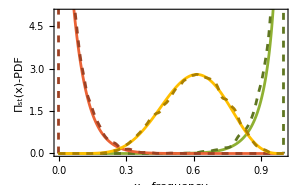

./Documents/Dominance/DominancePlotsBiased01.svg

```mathematica
getPlotData[α_,β_,ϵ_,δ_,λ_, color_]:=Block[{left, right, C1, tab, tab2},
left=err+0;
right=-err+1;
C1 = NIntegrate[Π[t,α,β,ϵ,λ,δ], {t,left,right}] ;
tab =Table[{x,Π[x,α,β,ϵ,λ,δ]/C1}, {x, left+10^-14, right-10^-14, 0.001}];
tab2 = RunSimulationHist[{{ α,β, ϵ,0, δ,λ, 0  }}, numInvoc, 0, 1];

Show[
ListLinePlot[tab, PlotStyle->{ColorData[97,color]},PlotRange->{{0, 1},Full}], SmoothHistogram[tab2, 0.01, "PDF", PlotStyle->{Darker[ColorData[97,color]], Dashed},PlotRange->{{0, 1}, Full}]]
];

plt=Show[getPlotData[0.1, 0.3, 0.6, -0.18, 10.0,3],
getPlotData[0.1, 0.3, 0.6, -0.48, 10.0,4],
getPlotData[0.1, 0.3, 0.6, -0.3, 10.0,8], PlotRange->{Full, {0, 5}}, Frame->True, FrameLabel->{"x - frequency", "Π_st(x)-PDF"}, BaseStyle->{FontSize->14}, ImageSize->300]

Export["./Documents/Dominance/DominancePlotsBiased01.svg", plt]
```

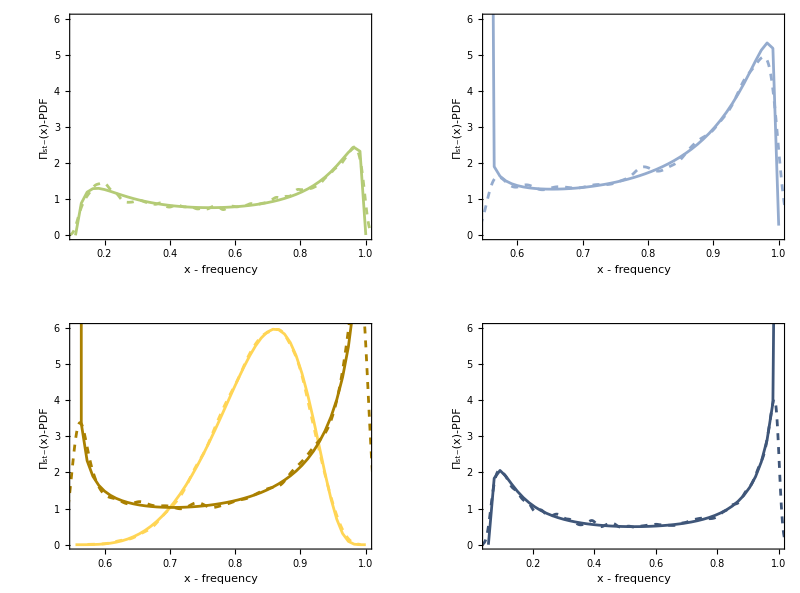

./Documents/Dominance/DominancePlotsAsym02.svg

```mathematica
numInvoc=10000;
getPlotData[α_,β_,ϵ_,δ_,λ_, color_]:=Block[{left, right, C1, tab, tab2},
left=err+(β-ϵ)/(β-α);
right=-err+1;
C1 = NIntegrate[Πas[t,α,β,ϵ,λ,δ], {t,left,right}] ;
tab =Table[{x,Πas[x,α,β,ϵ,λ,δ]/C1}, {x, left, right, (right-left)/50}];
tab2 = RunSimulationHist[{{ α,β, ϵ,1, δ,λ, 0  }}, numInvoc, 0, 1];

Show[
ListLinePlot[tab, PlotStyle->{color}, PlotRange->{{left, right},Full}],
SmoothHistogram[tab2, 0.01, "PDF", PlotStyle->{color, Dashed}],
Frame->True, FrameLabel->{"x - frequency", "Π_(st-)(x)-PDF"}, BaseStyle->{FontSize->14}, ImageSize->200, PlotRange->{{left, right},{0, 6}}]
];


mShapePlot = getPlotData[0.1, 1.0, 0.9, 0, 0.17,Lighter[ColorData[97,3]]];
uShapePlot = getPlotData[0.1, 1.0, 0.5, 0, 0.1,Darker[ColorData[97,8]]];
leftInfPlot = getPlotData[0.1, 1.0, 0.5, 0, 0.17,Lighter[ColorData[97,1]]]; 
rightInfPlot = getPlotData[0.1, 1.0, 0.95, 0, 0.1,Darker[ColorData[97,1]]];
bellShapePlot = getPlotData[0.1, 1.0, 0.5, 0, 1.0,Lighter[ColorData[97,8]]];
plt=GraphicsGrid[{{mShapePlot, leftInfPlot}, {Show[bellShapePlot, uShapePlot], rightInfPlot}}]

Export["./Documents/Dominance/DominancePlotsAsym02.svg", plt]
```